# Tandem Solar Cell Model

Copyright 2017 Moritz H. Futscher, Bruno Ehlrer
AMOLF, Center for Nanophotonics
Science Park 105
1098 XG, Amsterdam
The Netherlands

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or (at your option) any later version.

This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU General Public License for more details.

You should have received a copy of the GNU General Public License along with this program. If not, see <http://www.gnu.org/licenses/>.

This program models a silicon solar cell with an efficiency of 26.7% and a perovskite solar cell with an efficiency of 19.7%. These two subcells are then used to simulate the efficiency of a perovskite/Si tandem solar cell under standard test conditions. By using measured solar spectra and temperatures data this model can be extended to simulate the performance of realistic perovskite/Si tandem solar cells under real world climate conditions. Measured solar spectra and temperatures can be downloaded for example from NREL at https://midcdmz.nrel.gov/apps/go2url.pl?site=BMS&page=spectra.pl?BMS and will soon be avalible from AMOLF at http://www.lmpv.nl/solar-field/

The procedure is based on work of:
*) W. Shockley and H. J. Queisser, Detailed Balance Limit of Efficiency of p-n Junction Solar Cells. J. Appl. Phys. 1961, 32, 510-519 DOI: 10.1063/1.1736034.
*) A. De Vos, Detailed Balance Limit of the Efficiency of Tandem Solar Cells. J. Phys. D. Appl. Phys. 1980, 13, 839-849 DOI: 10.1088/0022-3727/13/5/018.
*) R. Strandberg, Detailed Balance Analysis of Area De-Coupled Double Tandem Photovoltaic Modules. Appl. Phys. Lett. 2015, 106, 33902 DOI: 10.1063/1.4906602.
*) J. Nelson, The Physics of Solar Cells; Imperial College Press, 2003.
*) M. H. Futscher and B. Ehrler, Efficiency Limit of Perovskite/Si Tandem Solar Cells. ACS Energy Lett. 2016, 1, 863-868 DOI: 10.1021/acsenergylett.6b00405.

When citing this work, please refer to:
M. H. Futscher, B. Ehrler, Modeling the Performance Limitations and Prospects of Perovskite/Si Tandem Solar Cells under Realistic Operating Conditions, ACS Energy Lett. 2017, DOI: 10.1021/acsenergylett.7b00596

## Input parameters

## Constants

```mathematica
c = 299792458.; (* units: m / s *)
h = 6.6260695729*10^-34; (* units: J s - Planck's Constant *)
h2 = 4.136 10^-15; (* units: eV s - Planck's Constant *)
q = 1.60217657*10^-19; (* units: Coulombs *)
k = 8.617 * 10^−5; (* units: eV / K *)
T = 298.15;(* units: K *)
fac = h c 10^9 /q (* coevert nm to eV *);
k2= 1.3807 10^-23 (*J/K*);
```

## Standard solar spectrum

```mathematica
(* Import ASTM G173-03 Reference Spectra *)
(* downloaded from http://rredc.nrel.gov/solar/spectra/am1.5/astmg173/astmg173.html *)
AM1p5global = Drop[Import[NotebookDirectory[] <> "Input/ASTMG173.xls"][[2, All, {1, 3}]], 2];
```

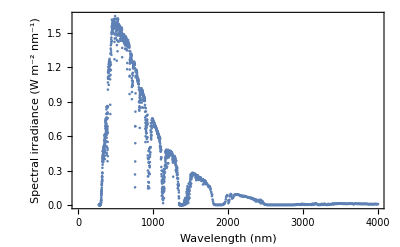

```mathematica
ListPlot[AM1p5global,Frame->True,FrameLabel->{"Wavelength (nm)","Spectral irradiance (W m^-2 nm^-1)"}]
```

```mathematica
(* Calculate the solar irradiance of the solar spectrum *)
(* units: W/m^2 *)
PowerofSun = Quiet[Integrate[Interpolation[AM1p5global][wl],{wl,AM1p5global[[1,1]],AM1p5global[[-1,1]]}]]
```

1000.38

```mathematica
(* Function to calculate the flux of a solar spectrum *)
(* units: A/(m^2 eV) *)
makeFlux[data_]:={fac/#[[1]],h c/(fac/#[[1]])^2 #[[1]]/(h c) #[[2]]}&/@data;
```

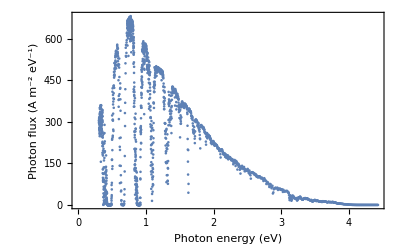

```mathematica
ListPlot[makeFlux[AM1p5global],Frame->True,FrameLabel->{"Photon energy (eV)","Photon flux (A m^-2 eV^-1)"}]
```

```mathematica
(* Photon flux at a certain photon energy *)
(* units: A/(m^2 eV) *)
Γ[En_]:=Interpolation[makeFlux[AM1p5global]][En];
```

## Silicon solar cell

The Si solar cell is modeled by fitting the current-voltage characteristics of a 26.7% efficient Si solar cell. The EQE of the Si solar cell is used to account for optical losses and parasitic absorption. The date for the JV curve and for the EQE are from M. A. Green  et al. Solar Cell Efficiency Tables (Version 50). Prog. Photovoltaics Res. Appl. 2017, 25, 668-676 DOI: 10.1002/pip.2909.

Functions

```mathematica
(* Temperature dependent intrinsic charge carrier concentration from K. Misiakos, et al. Accurate Measurements of the Silicon Intrinsic Carrier Density from 78 to 340 K. J.Appl.Phys. 1993, 74, 3293–3297 DOI:10.1063/1.354551 *)
(* units: m^-3 *)
Sini[T_] := 5.29 10^19 (T/300.)^2.54 Exp[-6726./T]*10^6
```

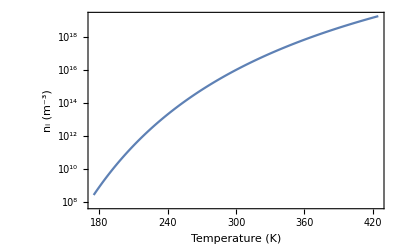

```mathematica
ListLogPlot[Table[{T,Sini[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","n_i (m^-3)"}]
```

```mathematica
(* Temperature dependent bandgap is calculated using Varshni’s empirical equation with values from the book Physics of Semiconductor Devices Physics of Semiconductor Devices, Wiley-Interscience, 1995 from Sze *)
(* units: eV *)
SiBandgap[T_] := 1.17 - 4.73 10^-4 T^2./(T+636.)
```

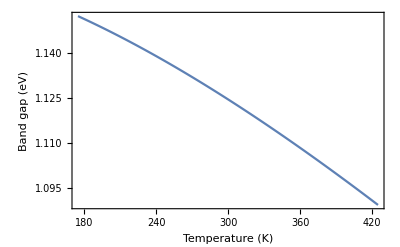

```mathematica
ListPlot[Table[{T,SiBandgap[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Band gap (eV)"}]
```

```mathematica
(* Temperature dependent Auger coefficient from J. Dziewior et al. Auger Coefficients for Highly Doped and Highly Excited Silicon. Appl.Phys.Lett. 1977, 346, 11–14 DOI:10.1063/1.89694 *)
(* units: 10^43 m^6/s *)
SiC[T_] :=3.79*10^-43*(T/300.)^(1./2.)
```

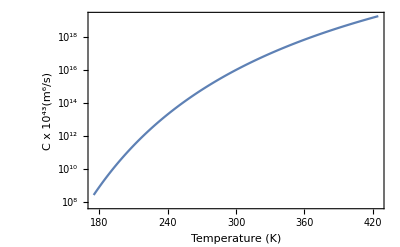

```mathematica
ListLogPlot[Table[{T,Sini[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","C x 10^43(m^6/s)"}]
```

Import JV and EQE

To account for spectral regions outside the published range, the regions below 300 and above 1200 nm were set to 0 % EQE.

```mathematica
(* Import JV characteristic*)
RecordSi = Import[NotebookDirectory[] <> "Input/Si.csv"];
```

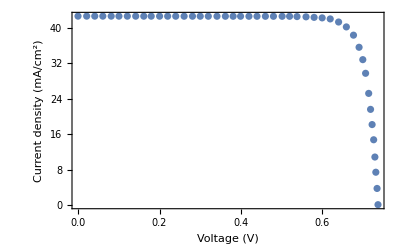

```mathematica
ListPlot[RecordSi,Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

```mathematica
(* Import EQE *)
RecordSiEQE = Import[NotebookDirectory[] <> "Input/Si_EQE.csv"];
EQESi = Interpolation[RecordSiEQE,InterpolationOrder->1];
```

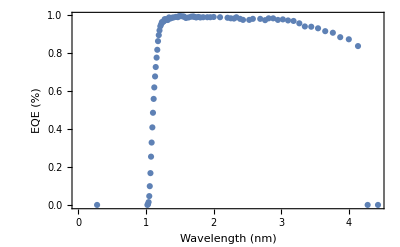

```mathematica
ListPlot[RecordSiEQE,Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"}]
```

Current densities

```mathematica
(* Generation current density *)
jgSi = Quiet[NIntegrate[ EQESi[En] Γ[En],{En,0.8,4.4}]];
```

```mathematica
(* Radiative recombination current density *)
JRad0Si = q 2 Pi/(c^2 h2^3)NIntegrate[  En^2/(Exp[En/( k T)]-1),{En,SiBandgap[T],4.4}];
JRSi[V_,Il_,Rs_]:=JRad0Si ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Auger recombination current density *)
JRAuger[V_,Il_,Rs_] :=  q L SiC[T] Sini[T]^3( Exp[(3 (V+Il*Rs*0.0001))/(2 k T)]-1);
```

```mathematica
(* Non-radiative recombination current density *)
JRnonSi[V_,Il_,Rs_] :=1.88485*10^-42 Sini[T]^2(Exp[(V+Il*Rs*0.0001)/( k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Silicon cell model

```mathematica
(* Thickness of Si *)
(* units: m *)
L = 2.0*10^-4;
```

```mathematica
(* Parasitic resistances of Si cell *)
(* units: Ω cm^2 *)
RsSi = 0.08;
RshSi = 10000.;
```

```mathematica
(* Record Si Single-Junction *)
SQSi[Eg1_]:=Quiet[{

(* a = 0.01 pA/cm^2 *)
(* Rsh = 10000 ohm cm^2 *)
(* Rs = 0.08 ohm cm^2 *)
(* n = 1 *)

(* Make JV characteristic *)
dSi=Table[{v1,
FindRoot[
Il==jgSi-
JRSi[v1,Il,RsSi]-
JRAuger[v1,Il,RsSi]- 
JRnonSi[v1,Il,RsSi]-
Resistance[v1,Il,RsSi,RshSi]
,{Il,0}][[1,2]]},{v1,0,Eg1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc *)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];

(* Calculate Jsc *)
jscSi=ivSi[0]/10;

(* Finding the maximum power conversion efficiency *)
NMaximize[{100ivSi[V] V/PowerofSun,0<V<Eg1},V]}][[1,1]];
```

Calculate efficiency

```mathematica
(* Model Si cell *)
"Efficiency: "<> ToString[Round[SQSi[SiBandgap[T]],0.1]] <>"%"
"Jsc: "<> ToString[Round[jscSi,0.01]]<> " mA/cm^2"
"Voc: "<> ToString[Round[vocSi,0.001]]<> " V"
"FF: "<> ToString[Round[N[NMaximize[{Interpolation[dSi][v] v,0<v<0.8},v][[1]]]/(jscSi*vocSi)*10,0.1]]<> "%"
```

Efficiency: 26.7%

Jsc: 42.65 mA/cm^2

Voc: 0.738 V

FF: 84.9%

```mathematica
devide[input_] := Table[{V,input[V]/10},{V,0,0.9,0.01}];
```

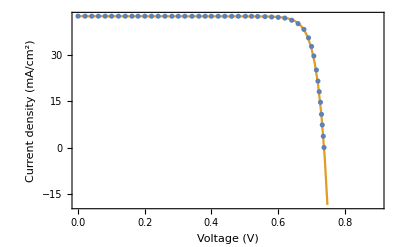

```mathematica
ListPlot[{RecordSi,ivSi//devide},Joined->{False,True},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

## Perovskite solar cell

The Perovskite solar cell is modeled by fitting the current-voltage characteristics of a 19.7% efficient perovskite solar cell based on a formamidinium lead iodide and methylammonium lead iodide mixture with a bandgap of 1.49 eV. The EQE of the perovskite solar cell is used to account for optical losses and parasitic absorption. The date for the JV curve and for the EQE are from M. A. Green  et al. Solar Cell Efficiency Tables (Version 48). Prog. Photovoltaics Res. Appl. 2016, 24, 905-913 DOI: 10.1002/pip.2788.

Functions

```mathematica
(* Temperature dependent bandgap from W. A. Saidi et al. Temperature Dependence of the Energy Levels of Methylammonium Lead Iodide Perovskite from First Principles. J.Phys.Chem.Lett. 2016, 7, 5247–5252 DOI:10.1021/acs.jpclett.6b02560.*)
(* units: eV *)
PerovskiteBandgap[T_] := 1.3856475+ 0.00035*T
```

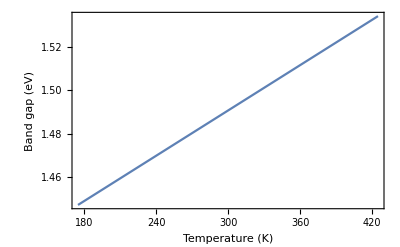

```mathematica
ListPlot[Table[{T,PerovskiteBandgap[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Band gap (eV)"}]
```

```mathematica
(* The temperature dependent intrinsic charge carrier concentration is calculated assuming that the dinsity of states in the conduction band and in the valance band at 25 °C are Subscript[N, C]=Subscript[N, V]=3.97 10^18 cm^-3. *)
(* units: m^-3 *)
Perovskiteni[T_]  := 7.361850425998709*^20*T^(3/2)*Exp[-PerovskiteBandgap[T]/(2 k T)]
```

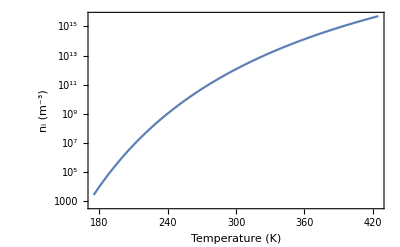

```mathematica
ListLogPlot[Table[{T,Perovskiteni[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","n_i (m^-3)"}]
```

```mathematica
(* Temperature deendent built-in bias *)
(* units: V *)
PerovskiteVbi[T_] := (k2 T)/q *Log[E,8.786724134893697*^45/Perovskiteni[T]^2]
```

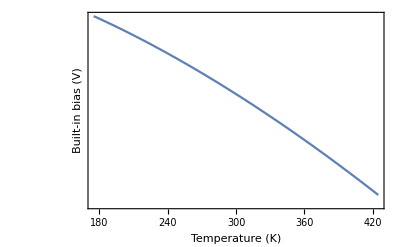

```mathematica
ListLogPlot[Table[{T,PerovskiteVbi[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Temperature (K)","Built-in bias (V)"}]
```

```mathematica
(* The intensity dependent charge carrier lifetime is obtained by fitting experimental data from D. W. DeQuilettes et al.Impact of Microstructure on Local Carrier Lifetime in Perovskite Solar Cells.Science 2015, 348, 683–686 DOI:10.1126/science.aaa5333.*)
(* units: μs *)
PerovskiteT[Irradiation_]  :=2.63041*Irradiation^(-0.14)
```

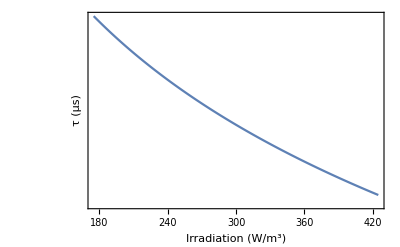

```mathematica
ListLogPlot[Table[{T,PerovskiteT[T]},{T,175,425}],Joined->True,Frame->True,FrameLabel->{"Irradiation (W/m^3)","τ (μs)"}]
```

Import JV and EQE

To account for spectral regions outside the published range, the regions below 300 and above 900 nm were set to 0 % EQE.

```mathematica
(* Import JV characteristic*)
RecordPerovskiteForward = Import[NotebookDirectory[] <> "Input/Perovskite_Forward.csv"];
RecordPerovskiteReverse = Import[NotebookDirectory[] <> "Input/Perovskite_Reverse.csv"];
```

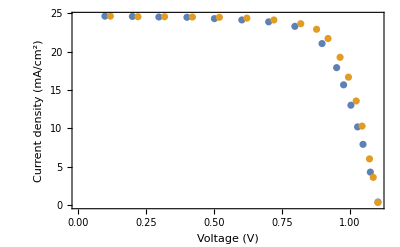

```mathematica
ListPlot[{RecordPerovskiteForward,RecordPerovskiteReverse},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

```mathematica
(* Import EQE *)
RecordPerovskiteEQE = Import[NotebookDirectory[] <> "Input/Perovskite_EQE.csv"];
EQEPerovskite = Interpolation[RecordPerovskiteEQE,InterpolationOrder->1];
```

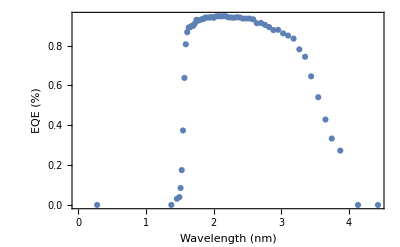

```mathematica
ListPlot[EQEPerovskite,Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"}]
```

Current densities

```mathematica
(* Generation current density *)
jgPerovskite = Quiet[NIntegrate[ EQEPerovskite[En] Γ[En],{En,0,4.4}]];
```

```mathematica
(* Radiative recombination current density *)
JRad0Perovskite = q 2 Pi/(c^2 h2^3)NIntegrate[  En^2/(Exp[En/( k T)]-1),{En,PerovskiteBandgap[T],4.4}];
JRPerovskite[V_,Il_,Rs_]:=JRad0Perovskite ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Non-radiative recombination current density *)
JRnonPerovskite[V_,Il_,Rs_] :=2.58719*10^-19 Perovskiteni[T] Re[Sqrt[(PerovskiteVbi[T]-V)]]/PerovskiteT[PowerofSun](Exp[(V+Il*Rs*0.0001)/(2 k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Perovskite cell model

```mathematica
(* Parasitic resistances of perovskite cell *)
(* units: Ω cm^2 *)
RsPerovskite = 3.10;
RshPerovskite = 1500.;
```

```mathematica
(* Record Perovskite Single-Junction *)
SQPerovskite[Eg1_]:=Quiet[{

(* a = 28.5 pA/cm^2 *)
(* Rsh = 1600 ohm cm^2 *)
(* Rs = 3.10 ohm cm^2 *)
(* n = 2.0 *)

(* Make JV characteristic *)
dPerovskite=Table[{v1,FindRoot[Il==jgPerovskite-
JRPerovskite[v1,Il,RsPerovskite]-
JRnonPerovskite[v1,Il,RsPerovskite]-
Resistance[v1,Il,RsPerovskite,RshPerovskite]
,{Il,0}][[1,2]]},{v1,0,Eg1,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc *)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg1-0.2}][[1,2]];

(* Calculate Jsc *)
jscPerovskite=ivPerovskite[0]/10;

(* Finding the maximum power conversion efficiency *)
NMaximize[{100ivPerovskite[V] V/PowerofSun,0<V<Eg1},V]}][[1,1]];
```

Calculate efficiency

```mathematica
(* Model perovskite cell *)
"Efficiency: "<> ToString[Round[SQPerovskite[PerovskiteBandgap[T]],0.1]] <>"%"
"Jsc: "<> ToString[Round[jscPerovskite,0.01]]<> " mA/cm^2"
"Voc: "<> ToString[Round[vocPerovskite,0.001]]<> " V"
"FF: "<> ToString[Round[N[NMaximize[{Interpolation[dPerovskite][v] v,0<v<1},v][[1]]]/(jscPerovskite*vocPerovskite)*10,0.1]]<> "%"
```

Efficiency: 19.7%

Jsc: 24.67 mA/cm^2

Voc: 1.104 V

FF: 72.3%

```mathematica
devide[input_] := Table[{V,input[V]/10},{V,0,1.2,0.01}];
```

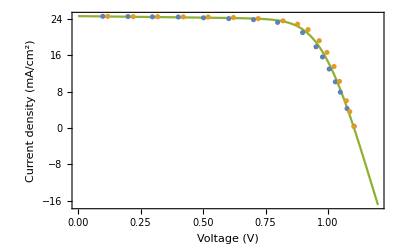

```mathematica
ListPlot[{RecordPerovskiteForward,RecordPerovskiteReverse,ivPerovskite//devide},Joined->{False,False,True},Frame->True,FrameLabel->{"Voltage (V)","Current density (mA/cm^2)"}]
```

## Perovskite/silicon tandem solar cell

Optical model

Optical losses are included by fitting a Gaussian distribution to the onset of the perovskite EQE. 10 % of the light with an energy below the Gaussian distribution is assumed to be absorbed by parasitic absorption. A small fraction of light between the bandgap and 600 nm that is transmitted is included to follow published transmission curves such as from B. Chen et al. Efficient Semitransparent Perovskite Solar Cells for 23.0%-Efficiency Perovskite/Silicon Four-Terminal Tandem Cells. Adv. Energy Mater. 2016, 6, 1601128 DOI: 10.1002/aenm.201601128.

```mathematica
(* Fit Gaussian *)
model[x_]=0.119068Evaluate[PDF[NormalDistribution[x0,sigma],x]];
data = Table[{i,EQEPerovskite[i]},{i,1.35,1.62,0.05}];
fit=FindFit[data,model[x],{x0,sigma},x];
```

```mathematica
(* Transmitted light to silicon bottom cell *)
TransmittedtoSi = Interpolation[Join[Table[{x,0.1+model[x]/.fit},{x,0.8,1.595,0.01}],Table[{i,Fit[{{1.595,0.1+model[1.595]/. fit},{2,1}},{1,x},x]/.x->i},{i,1.6,2,0.01}],Table[{x,1},{x,2.01,4,0.01}]],InterpolationOrder->1];
```

```mathematica
(* EQE of Si back cell *)
EQESiback =Interpolation[Replace[Table[{x,EQESi[x]-TransmittedtoSi[x]},{x,0.8,3.5,0.01}],n_?(#<0&)->0,{2}],InterpolationOrder->1];
```

```mathematica
Backtowavelangth[data_] := Table[{fac/wl,data[wl]},{wl,0.8,4,0.01}];
```

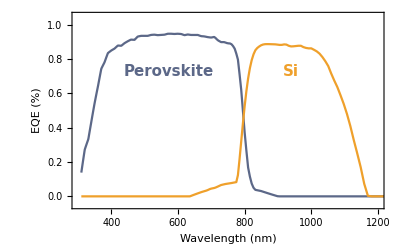

```mathematica
Quiet[Show[ListPlot[{EQEPerovskite//Backtowavelangth,EQESiback//Backtowavelangth},Joined->{True,True,True},Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"},
PlotStyle->{ColorData[10,8],ColorData[10,3],GrayLevel[0.5]},
PlotRange->{{300,1200},{-0.05,1.05}}],

Epilog->{
Inset[Style["Perovskite",ColorData[10,8],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.31,0.70}]],
Inset[Style["Si",ColorData[10,3],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.70,0.7}]]
}]]
```

```mathematica
(* Optical thickness of perovskite top cell. This value has to be optimized in order to current-match the silicon bottom cell with the perovskite top cell *)
thick=0.82;
```

```mathematica
(* Transmitted light to silicon bottom cell when using an optically-thin perovskite top cell *)
TransmittedtoSithin = Interpolation[Join[Table[{x,0.1+thick*(model[x]/.fit)},{x,0.8,1.595,0.01}],Table[{i,(Fit[{{1.595,0.1+model[1.595]/. fit},{2,1}},{1,x},x]/.x->i)*thick},{i,1.60,2,0.01}],Table[{x,thick*1},{x,2.01,4,0.01}]],InterpolationOrder->1];
```

```mathematica
(* EQE of Si back cell when using an optically-thin perovskite top cell *)
EQESibackthin =Interpolation[Replace[Table[{x,EQESi[x]-TransmittedtoSithin[x]},{x,0.8,4,0.01}],n_?(#<0&)->0,{2}],InterpolationOrder->1];
```

```mathematica
(* EQE of optically-thin perovskite top cell *)
EQEPerovskitethin =Interpolation[Table[{x,EQEPerovskite[x]*thick},{x,0.8,4.4,0.01}],InterpolationOrder->1];
```

```mathematica
plottransmited = Interpolation[Table[{x,1-1*TransmittedtoSi[x]},{x,0.8,4,0.01}]];
```

```mathematica
plottransmitedthin = Interpolation[Table[{x,1-1*TransmittedtoSithin[x]},{x,0.8,4,0.01}]];
```

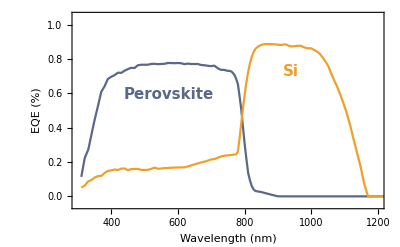

```mathematica
Quiet[Show[ListPlot[{EQEPerovskitethin//Backtowavelangth,EQESibackthin//Backtowavelangth},Joined->True,Frame->True,FrameLabel->{"Wavelength (nm)","EQE (%)"},
PlotStyle->{ColorData[10,8],ColorData[10,3],GrayLevel[0.5]},PlotRange->{{300,1200},{-0.05,1.05}}],

Epilog->{
Inset[Style["Perovskite",ColorData[10,8],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.31,0.58}]],
Inset[Style["Si",ColorData[10,3],Bold,FontFamily->"Helvetica",FontSize->15,Background->White],Scaled[{0.70,0.7}]]}]]
```

Current densities

```mathematica
(* Calculate generation current densities *)
jgPerovskitetandem =Quiet[ NIntegrate[EQEPerovskite[En] Γ[En],{En,1.2,4.4}]];
jgSitandem =Quiet[ NIntegrate[EQESiback[En] Γ[En],{En,0.8,3.5}]];
```

```mathematica
(* Calculate generation current densities for optical thin perovskite *)
jgPerovskitetandemthin = Quiet[ NIntegrate[ EQEPerovskitethin[En] Γ[En],{En,1.2,4.4}]];
jgSitandemthin = Quiet[ NIntegrate[ EQESibackthin[En] Γ[En],{En,0.8,3.5}]];
```

```mathematica
(* Radiative recombination current densities *)
JRPerovskite[V_,Il_,fg_,Rs_]:=fg JRad0Perovskite ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
JRSi[V_,Il_,fg_,Rs_]:=fg JRad0Si ( Exp[(V+Il*Rs*0.0001)/(k T)]-1);
```

```mathematica
(* Resistance *)
Resistance[V_,Il_,Rs_,Rsh_] := (V+Il *Rs*0.0001)/(Rsh*0.0001);
```

Tandem solar cell model

To model the tandem solar cells we assume a perfect reflector on the back side of the silicon bottom cell and no selective reflector between the perovskite top cell and the Si bottom cell.For simplicity we neglect reabsorption of luminescence between the two subcells.

### Current-matched series tandem

```mathematica
(* Realistic series tandem Limit *)
SQSeries[Eg1_,Eg2_]:=Quiet[{

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==jgSitandemthin-
JRSi[v1,Il1,1,RsSi]-
JRAuger[v1,Il1,RsSi]- 
JRnonSi[v1,Il1,RsSi]-
Resistance[v1,Il1,RsSi,RshSi]
,{Il1,0}][[1,2]]},{v1,0,Eg1-0.1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandemthin-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

ivCurve={};

(* Make series tandem JV characteristic *)
Do[{
d=Table[{v1,(ivSi[v1]-ivPerovskite[v2])^2},{v1,0,vocSi,.001}];
v1=Cases[d,{_,Min@d[[All,2]]}][[1,1]];AppendTo[ivCurve,{v1+v2,Min[ivPerovskite[v2],ivSi[v1]]}];Clear[v1]},{v2,0,vocPerovskite,.001}]

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 Interpolation[ivCurve][V] V/PowerofSun,First[ivCurve][[1]]<V<Last[ivCurve][[1]]},V][[1]]}][[1,1]];
```

### Voltage-matched module tandem

```mathematica
(* Realistic module tandem limit *)
SQModule[Eg1_,Eg2_,n_]:=Quiet[{
(* n.. number of bottom cells for each top cell *)

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==(jgSitandem-
JRSi[v1/n,Il1,1,RsSi]-
JRAuger[v1/n,Il1,RsSi]- 
JRnonSi[v1/n,Il1,RsSi]-
Resistance[v1/n,Il1,RsSi,RshSi])/n
,{Il1,0}][[1,2]]},{v1,0,(Eg1-0.1)*n,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,(Eg1-0.2)*n}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandem-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

(* Make JV-characteristic of module tandem *)
d = Table[{v,Interpolation[dSi][v]+Interpolation[dPerovskite][v]},{v,0,Eg2-0.2,0.001}];
iv=Interpolation[d];

(* Calculate Voc and Jsc of module tandem *)
voc=FindRoot[iv[v],{v,Eg2-0.3}][[1,2]];

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 iv[V] V/PowerofSun,0 <V<voc},V][[1]]}][[1]];
```

### Four-terminal tandem

```mathematica
(* Realistic four-terminal tandem limit *)
SQFour[Eg1_,Eg2_]:=Quiet[{

(* Make JV characteristic of Si bottom cell *)
dSi=Table[{v1,
FindRoot[
Il1==jgSitandem-
JRSi[v1,Il1,1,RsSi]-
JRAuger[v1,Il1,RsSi]- 
JRnonSi[v1,Il1,RsSi]-
Resistance[v1,Il1,RsSi,RshSi]
,{Il1,0}][[1,2]]},{v1,0,Eg1-0.1,.001}];
ivSi=Interpolation[dSi];

(* Calculate Voc and Jsc of Si bottom cell*)
vocSi=FindRoot[ivSi[v],{v,Eg1-0.2}][[1,2]];
jscSi = ivSi[0];

(* Make JV characteristic of perovskite top cell*)
dPerovskite=Table[{v2,
FindRoot[
Il2==jgPerovskitetandem-
JRPerovskite[v2,Il2,2,RsPerovskite]-
JRnonPerovskite[v2,Il2,RsPerovskite]-
Resistance[v2,Il2,RsPerovskite,RshPerovskite]
,{Il2,0}][[1,2]]},{v2,0,Eg2-0.2,.001}];
ivPerovskite=Interpolation[dPerovskite];

(* Calculate Voc and Jsc of perovskite top cell*)
vocPerovskite=FindRoot[ivPerovskite[v],{v,Eg2-0.3}][[1,2]];
jscPerovskite = ivPerovskite[0];

(* Finding the maximum power conversion efficiency *)
NMaximize[{100 ivSi[V] V/PowerofSun,0<V<vocSi},V][[1]]+NMaximize[{100 ivPerovskite[V] V/PowerofSun,0 <V<vocPerovskite},V][[1]]}][[1]];
```

Calculate efficiencies

```mathematica
(* Model perovskite/Si tandem solar cells *)
"Series tandem: "<> ToString[Round[SQSeries[SiBandgap[T],PerovskiteBandgap[T]],0.1]] <>"%"
"Module tandem: "<> ToString[Round[SQModule[SiBandgap[T],PerovskiteBandgap[T],1.39],0.1]] <>"%"
"Four-terminal tandem: "<> ToString[Round[SQFour[SiBandgap[T],PerovskiteBandgap[T]],0.1]] <>"%"
```

Series tandem: 27.6%

Module tandem: 28.5%

Four-terminal tandem: 28.5%